# CO2 Phase Diagram

## PC-SAFT (Perturbed-Chain Statistical Associating Fluid Theory)

Andy Ylitalo, with guidance from Dr. Huikuan Chao and mentorship from Prof. Zhen-Gang Wang

## Questions

## 0. Setup

```mathematica
SetDirectory[FileNameJoin[{"C:","Users","Andy.DESKTOP-CFRG05F","OneDrive - California Institute of Technology", "Documents", "Research", "Wang", "PC-SAFT"}]];
```

## 1. Equations

```mathematica
d[σ_,β_,ϵ_]:=σ(1-0.12Exp[-3ϵ β]);  (* temperature-dependent particle diameter, Gross and Sadowski (2001) *)
```

Note that ξ[ρ,σ,3] represents the total packing fraction and is therefore dimensionless. In general, ξ[ρ,σ,n] has dimensions of (length)^(n-3).

```mathematica
ξ[ρCO2_,ρC5_,dCO2_,dC5_,j_]:=π/6( ρCO2 dCO2^j + ρC5 dC5^j);
```

### Free energy of ideal gas

```mathematica
βfIG[ρ_,N_]:= ρ/N(Log[ρ /N ]-1);
```

Cubed expression is the thermal de Broglie wavelength, λT = h / Sqrt[2 π m k T]. m is the mass of a single particle (in this case, CO2 atom, kg). Note that ρ is divided by N to get the density of molecules, not segments.
7.31*^-26 kg is the mass of a carbon dioxide atom (44.01 amu).

### Free energy of hard-sphere liquid

```mathematica
βfHS[ρCO2_,ρC5_,dCO2_,dC5_]:=6/π( (3 ξ[ρCO2,ρC5,dCO2,dC5,1]ξ[ρCO2,ρC5,dCO2,dC5,2])/(1-ξ[ρCO2,ρC5,dCO2,dC5,3])
+ (ξ[ρCO2,ρC5,dCO2,dC5,2])^3/(ξ[ρCO2,ρC5,dCO2,dC5,3](1-ξ[ρCO2,ρC5,dCO2,dC5,3])^2)
+ ((ξ[ρCO2,ρC5,dCO2,dC5,2])^3/(ξ[ρCO2,ρC5,dCO2,dC5,3])^2-ξ[ρCO2,ρC5,dCO2,dC5,0])Log[1-ξ[ρCO2,ρC5,dCO2,dC5,3]] );
```

### Free energy of association

```mathematica
gCO2[ρCO2_,ρC5_,dCO2_,dC5_]:=1/(1-ξ[ρCO2,ρC5,dCO2,dC5,3])+ 3ξ[ρCO2,ρC5,dCO2,dC5,2] dCO2/ (2(1-ξ[ρCO2,ρC5,dCO2,dC5,3])^2)+ (ξ[ρCO2,ρC5,dCO2,dC5,2])^2dCO2^2 / (2(1-ξ[ρCO2,ρC5,dCO2,dC5,3])^3); 
gC5[ρCO2_,ρC5_,dCO2_,dC5_]:=1/(1-ξ[ρCO2,ρC5,dCO2,dC5,3])+ 3ξ[ρCO2,ρC5,dCO2,dC5,2] dC5/ (2(1-ξ[ρCO2,ρC5,dCO2,dC5,3])^2)+ (ξ[ρCO2,ρC5,dCO2,dC5,2])^2dC5^2 / (2(1-ξ[ρCO2,ρC5,dCO2,dC5,3])^3); (* radial pair distribution function for segments of component i in the hard-sphere system *)
```

```mathematica
βfAssoc[ρCO2_,ρC5_,dCO2_,dC5_,NCO2_,NC5_]:=-(NCO2-1)/NCO2 ρCO2 Log[gCO2[ρCO2,ρC5,dCO2,dC5]]-(NC5-1)/NC5 ρC5 Log[gC5[ρCO2,ρC5,dCO2,dC5]];
```

### Free energy of dispersion

First, load the constants for the polynomial approximation of the integrals I1 and I2 in Gross and Sadowski (2001). We refer to them here as J1 and J2 according to the nomenclature used by Xu et al. (2012).

```mathematica
JConstants=Import[FileNameJoin[{"Data","J_integral_const_a_b.csv"}]];
```

```mathematica
a0=JConstants[[2;;-1, 2]];
a1 = JConstants[[2;;-1, 3]];
a2 = JConstants[[2;;-1, 4]];
b0 = JConstants[[2;;-1, 5]];
b1 = JConstants[[2;;-1, 6]];
b2 = JConstants[[2;;-1, 7]];
```

```mathematica
J1[ρCO2_,ρC5_,dCO2_,dC5_,Nbar_]:=Sum[ (a0[[i]] +(Nbar-1)/Nbar a1[[i]] + (Nbar-1)/Nbar (Nbar-2)/Nbar a2[[i]])(ξ[ρCO2,ρC5,dCO2,dC5,3])^(i-1),{i,1,Length[a]}]
J2[ρCO2_,ρC5_,dCO2_,dC5_,Nbar_]:=Sum[(b0[[i]] +(Nbar-1)/Nbar b1[[i]] + (Nbar-1)/Nbar (Nbar-2)/Nbar b2[[i]])(ξ[ρCO2,ρC5,dCO2,dC5,3])^(i-1),{i,1,Length[b]}]
```

```mathematica
M[ρCO2_,ρC5_,dCO2_,dC5_,Nbar_]:=1+Nbar(8 ξ[ρCO2,ρC5,dCO2,dC5,3] - 2 (ξ[ρCO2,ρC5,dCO2,dC5,3])^2)/(1-ξ[ρCO2,ρC5,dCO2,dC5,3])^4+ (1-Nbar)(20 ξ[ρCO2,ρC5,dCO2,dC5,3] - 27(ξ[ρCO2,ρC5,dCO2,dC5,3])^2 + 12 (ξ[ρCO2,ρC5,dCO2,dC5,3])^3 - 2(ξ[ρCO2,ρC5,dCO2,dC5,3])^4)/((1-ξ[ρCO2,ρC5,dCO2,dC5,3])^2(2-ξ[ρCO2,ρC5,dCO2,dC5,3])^2);
```

```mathematica
ϵij[ϵi_,ϵj_,kij_]:=Sqrt[ϵi ϵj](1-kij);
σij[σi_,σj_]:=(σi+σj)/2;
```

```mathematica
βfDisp[ρCO2_,ρC5_,σCO2_,σC5_,ϵCO2_,ϵC5_,kCO2C5_,Nbar_,β_]:=(-π ρCO2^2 (2 J1[ρCO2,ρC5,d[σCO2,β,ϵCO2],d[σC5,β,ϵC5],Nbar] β ϵCO2 + Nbar /M[ρCO2,ρC5,d[σCO2,β,ϵCO2],d[σC5,β,ϵC5],Nbar] J2[ρCO2,ρC5,d[σCO2,β,ϵCO2],d[σC5,β,ϵC5],Nbar] (β ϵCO2)^2) σCO2^3)+(-π ρC5^2 (2 J1[ρCO2,ρC5,d[σCO2,β,ϵCO2],d[σC5,β,ϵC5],Nbar] β ϵC5 + Nbar /M[ρCO2,ρC5,d[σCO2,β,ϵCO2],d[σC5,β,ϵC5],Nbar] J2[ρCO2,ρC5,d[σCO2,β,ϵCO2],d[σC5,β,ϵC5],Nbar] (β ϵC5)^2) σC5^3)+2(-π ρCO2 ρC5 (2 J1[ρCO2,ρC5,d[σCO2,β,ϵCO2],d[σC5,β,ϵC5],Nbar] β ϵij[ϵCO2,ϵC5,kCO2C5] + Nbar /M[ρCO2,ρC5,d[σCO2,β,ϵCO2],d[σC5,β,ϵC5],Nbar] J2[ρCO2,ρC5,d[σCO2,β,ϵCO2],d[σC5,β,ϵC5],Nbar] (β ϵij[ϵCO2,ϵC5,kCO2C5])^2) (σij[σCO2,σC5])^3)
```

### Total Free Energy

```mathematica
Nbar[ρCO2_,ρC5_,NCO2_,NC5_]:=(NCO2 ρCO2 +NC5 ρC5)/(ρCO2+ρC5);
kij[ka_,kb_,β_]:=ka + kb/β;
```

```mathematica
βf[ρCO2_,ρC5_,σCO2_,σC5_,ϵCO2_,ϵC5_,kCO2C5a_,kCO2C5b_,NCO2_,NC5_,β_]:=βfIG[ρCO2,NCO2]+βfIG[ρC5,NC5]+βfHS[ρCO2,ρC5,d[σCO2,β,ϵCO2],d[σC5,β,ϵC5]]+βfAssoc[ρCO2,ρC5,d[σCO2,β,ϵCO2],d[σC5,β,ϵC5],NCO2,NC5]+βfDisp[ρCO2,ρC5,σCO2,σC5,ϵCO2,ϵC5,kij[kCO2C5a,kCO2C5b,β],Nbar[ρCO2,ρC5,NCO2,NC5],β];
```

### Chemical potential

```mathematica
βμCO2[ρCO2_,ρC5_,σCO2_,σC5_,ϵCO2_,ϵC5_,kCO2C5a_,kCO2C5b_,NCO2_,NC5_,β_]:=D[βf[ρCO2prime,ρC5,σCO2,σC5,ϵCO2,ϵC5,kCO2C5a,kCO2C5b,NCO2,NC5,β],ρCO2prime]/.ρCO2prime->ρCO2;
βμC5[ρCO2_,ρC5_,σCO2_,σC5_,ϵCO2_,ϵC5_,kCO2C5a_,kCO2C5b_,NCO2_,NC5_,β_]:=D[βf[ρCO2,ρC5prime,σCO2,σC5,ϵCO2,ϵC5,kCO2C5a,kCO2C5b,NCO2,NC5,β],ρC5prime]/.ρC5prime->ρC5;
```

### Pressure

```mathematica
βp[ρCO2_,ρC5_,σCO2_,σC5_,ϵCO2_,ϵC5_,kCO2C5a_,kCO2C5b_,NCO2_,NC5_,β_]:= -βf[ρCO2,ρC5,σCO2,σC5,ϵCO2,ϵC5,kCO2C5a,kCO2C5b,NCO2,NC5,β]+ρCO2 βμCO2[ρCO2,ρC5,σCO2,σC5,ϵCO2,ϵC5,kCO2C5a,kCO2C5b,NCO2,NC5,β]+ρC5 βμC5[ρCO2,ρC5,σCO2,σC5,ϵCO2,ϵC5,kCO2C5a,kCO2C5b,NCO2,NC5,β];
```

## 2. Plot

```mathematica
kB=1.38065*^-23;  (* Boltzmann constant [J/K] *)
T=290; (* temperature [K] *)
βParam=1/(kB T); (* beta parameter [1/J] *)
ϵCO2=170.5 kB; (* attractive well depth, from Xu et al. 2012 JCP [J] *)
σCO2= 2.79*^-10; (* bead size [m] *)
σCO2Ref = 1; (* use bead size as reference length for system *)
dCO2 = σCO2*(1-0.12*Exp[-3ϵCO2*βParam]); (* temperature-dependent particle diameter, Gross and Sadowski (2001) *)
ρmin=0; (* minimum mass density to plot[kg/m^3] *)
ρmax = 1100; (* maximum mass density to plot [kg/m^3] *)
NCO2 = 2; (* number of beads for one carbon dioxide molecule [nondim] *)
MBeadCO2= 0.044/NCO2; (* molar mass of one bead of carbon dioxide [kg/mol] *)
NA = 6.022*^23; (* Avogadro's number [molecules/mol] *)
ρCO2Conv=σCO2^3*NA/MBeadCO2; (* convert kg/m^3 -> molecules/kg *)
Pa2MPa = 1*^-6; (* multiplicative conversion from Pa -> MPa *)
pCO2Conv = Pa2MPa*βParam^(-1)*σCO2^(-3);
```

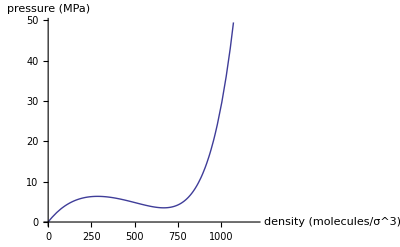

```mathematica
Plot[βp[ρ*ρCO2Conv,σCO2Ref,βParam,ϵCO2]*pCO2Conv,{ρ,ρmin, ρmax},AxesLabel->{"density (molecules/σ^3)","pressure (MPa)"}]
```

Plot in terms of kg/m^3

## 2. Numerical Solving

### Critical Point

Occurs where both first and second derivatives of pressure with respect to density are 0.

```mathematica
NSolve[{D[βp[ρ*ρCO2Conv,σCO2Ref,1/(kB Tc),ϵCO2],ρ]==0,D[D[βp[ρ*ρCO2Conv,σCO2Ref,1/(kB Tc),ϵCO2],ρ],ρ]==0},{ρ,Tc}]
```

$Aborted

## 3. Sanity Checks (thermodynamic relations)